```mathematica
Set 14: Graph Theory
```

## Graph creation

### Exercise Subsection

Create the Graph with vertices all subsets of Range@4 with an edge between two subsets if one contains the other (see Subsets and SubsetQ.)

### Exercise Subsection

Define a function that has input the integers n and m and output the graph with vertices Range@n and with an edge between two integers a and b if a^2 and b^2 are the same modulo m.  For this you many need to specify the vertices in Graph as well as the edges, see ?Graph for the syntax.

## Graph properties

### Exercise Subsection

The function GraphComplement[G] produces the graph with vertex set the same as G and with an edge between two vertices exactly when the edge does not exist in G.  Show that each graphs in the following list is isomorphic to its complement.

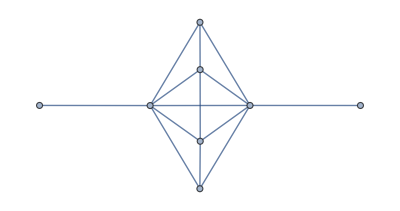
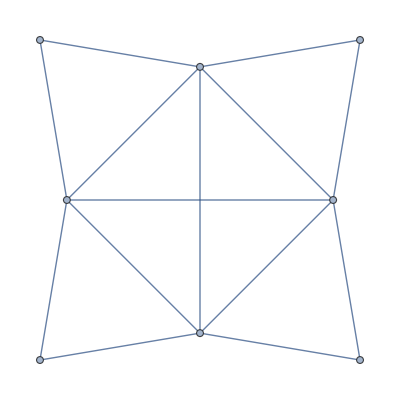
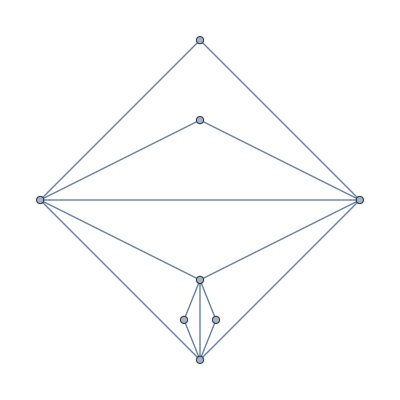
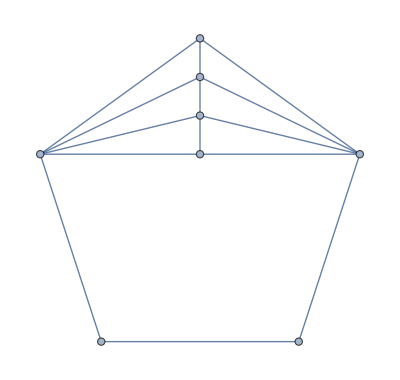
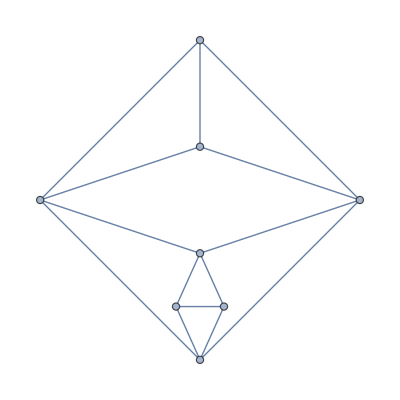
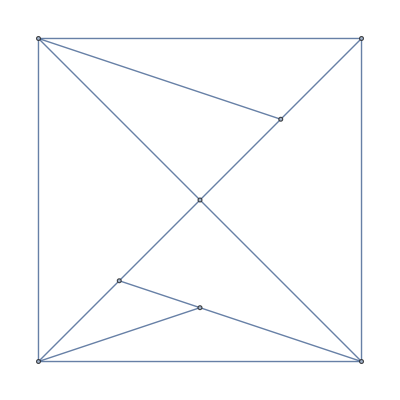
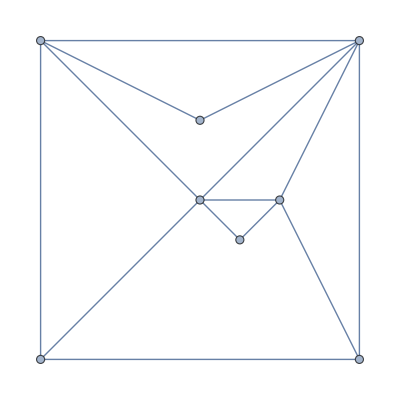
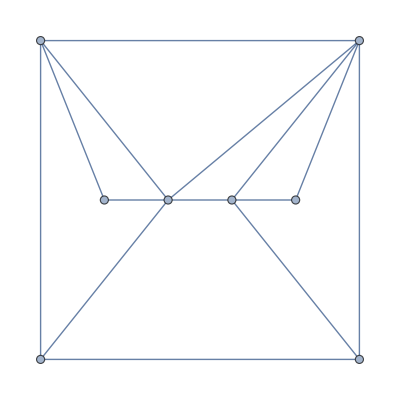
```mathematica
L={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

### Exercise Subsection

a. The function FindEdgeColoring[G] finds the optimal way to assign colors (positive integers) to the edges of G such that adjacent edges are different colors.  Use this function to color of the graph in the next cell.

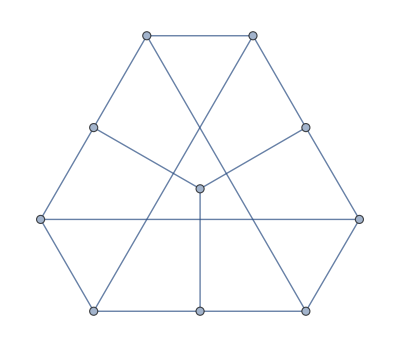
```mathematica
G=-Graphics-;
```

b . The function EdgeChromaticNumber[G] gives the minimum number of colors in such a coloring .  Estimate the average value of EdgeChromaticNumber for graphs with 25 vertices and 50 edges using RandomGraph .

### Exercise Subsection

A graph describing bordering states in the contiguous United States  is defined in the next cell.

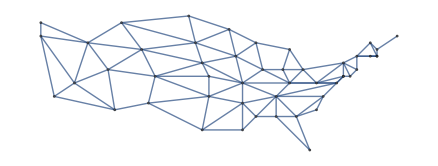

```mathematica
stateEdges={"CA"<->"NV","AZ"<->"NV","NV"<->"UT","ID"<->"NV","NV"<->"OR","CA"<->"OR","ID"<->"OR","OR"<->"WA","OK"<->"TX","LA"<->"TX","NM"<->"TX","AR"<->"TX","DC"<->"VA","DC"<->"MD","FL"<->"GA","AL"<->"FL","MA"<->"RI","CT"<->"RI","GA"<->"SC","NC"<->"SC","ID"<->"WA","AZ"<->"CA","CT"<->"MA","CT"<->"NY","DE"<->"MD","DE"<->"PA","DE"<->"NJ","LA"<->"MS","AR"<->"LA","IN"<->"MI","MI"<->"OH","MI"<->"WI","ND"<->"SD","MN"<->"ND","MT"<->"ND","ME"<->"NH","NH"<->"VT","MA"<->"NH","NJ"<->"NY","NJ"<->"PA","MA"<->"VT","NY"<->"VT","AL"<->"GA","AL"<->"MS","AL"<->"TN","AZ"<->"NM","AZ"<->"UT","IN"<->"OH","IL"<->"IN","IN"<->"KY","KS"<->"OK","CO"<->"KS","KS"<->"MO","KS"<->"NE","MD"<->"PA","MD"<->"VA","MD"<->"WV","MN"<->"WI","IA"<->"MN","MN"<->"SD","AR"<->"MS","MS"<->"TN","ID"<->"MT","MT"<->"WY","MT"<->"SD","NC"<->"VA","NC"<->"TN","GA"<->"NC","CO"<->"NM","NM"<->"OK","IL"<->"WI","IA"<->"WI","GA"<->"TN","IA"<->"IL","IL"<->"KY","IL"<->"MO","MA"<->"NY","NY"<->"PA","OH"<->"WV","OH"<->"PA","KY"<->"OH","CO"<->"UT","UT"<->"WY","ID"<->"UT","VA"<->"WV","TN"<->"VA","KY"<->"VA","PA"<->"WV","KY"<->"WV","AR"<->"OK","AR"<->"MO","AR"<->"TN","CO"<->"WY","CO"<->"NE","CO"<->"OK","IA"<->"SD","IA"<->"NE","IA"<->"MO","ID"<->"WY","NE"<->"WY","NE"<->"SD","MO"<->"NE","MO"<->"OK","SD"<->"WY","KY"<->"MO","KY"<->"TN","MO"<->"TN"};
stateCenters={"AL"->{-87,33},"AR"->{-92,35},"AZ"->{-111,34},"CA"->{-120,36},"CO"->{-105,39},"CT"->{-73,42},"DC"->{-77,39},"DE"->{-76,39},"FL"->{-82,28},"GA"->{-84,33},"IA"->{-93,42},"ID"->{-115,44},"IL"->{-89,40},"IN"->{-86,40},"KS"->{-97,39},"KY"->{-85,38},"LA"->{-92,31},"MA"->{-72,42},"MD"->{-77,39},"ME"->{-69,45},"MI"->{-85,43},"MN"->{-94,46},"MO"->{-92,38},"MS"->{-90,33},"MT"->{-110,47},"NC"->{-80,36},"ND"->{-100,48},"NE"->{-98,41},"NH"->{-72,43},"NJ"->{-75,40},"NM"->{-106,35},"NV"->{-117,38},"NY"->{-75,42},"OH"->{-83,40},"OK"->{-97,36},"OR"->{-122,45},"PA"->{-77,41},"RI"->{-72,42},"SC"->{-81,34},"SD"->{-99,44},"TN"->{-87,36},"TX"->{-98,31},"UT"->{-112,40},"VA"->{-78,38},"VT"->{-73,44},"WA"->{-122,47},"WI"->{-90,44},"WV"->{-81,38},"WY"->{-107,43}};G=Graph[First/@stateCenters,stateEdges,VertexCoordinates->stateCenters]
```

The function GraphDistance[G,u,v] finds the length of a shortest path from u to v in G.  The function FindShortestPath[G,u,v] finds one such path.  This path can then be visualized using a method similar to that below:

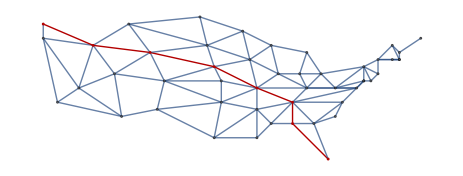

```mathematica
HighlightGraph[G,PathGraph@FindShortestPath[G,"WA","FL"]]
```

Define a function FarthestFrom[State1_] that inputs a State1, then finds a state State2 that is farthest from State1, and then outputs a highlighted graph showing a path from State1 to State2.

### Exercise Subsection

A cycle in a graph is a path that starts and ends at the same vertex.  FindCycles@G can find all cycles in G, for example, the next cell finds the maximum length cycle and displays in within a graph:

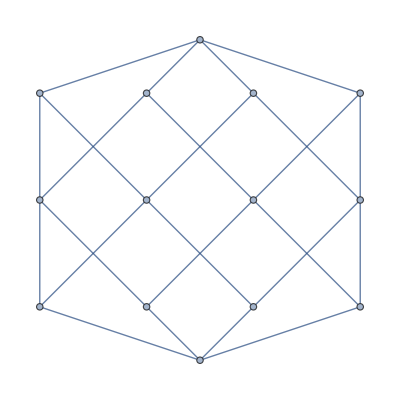
```mathematica
G=-Graphics-;
allcycles=FindCycle[G,Infinity,All];
cycle=First@FindCycle[G,Max[Length/@allcycles]];
HighlightGraph[G,PathGraph@cycle]
```

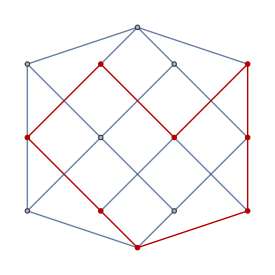

a. Write a function that has input a graph G and outputs the size of the maximum sized cycle in G.

b. Approximately what is the average size of the maximum cycle in a random graph with 12 vertices and 20 edges?

### Exercise Subsection

A graph is planar if it can be drawn in the plane without two edges crossing.  The function PlanarGraphQ tests if a graph is planar.

a. What is the approximate probability that a random graph with 50 edges and 50 vertices will be planar?

b. If graph is planar and connected, than the number of faces (this is the number of regions in the plane bounded by an edges) is 2-V+E where V is the number of vertices in the graph and E the number of edges (see VertexCount and EdgeCount).  Sort the following list (consider SortBy) by the number of faces in each planar graph.

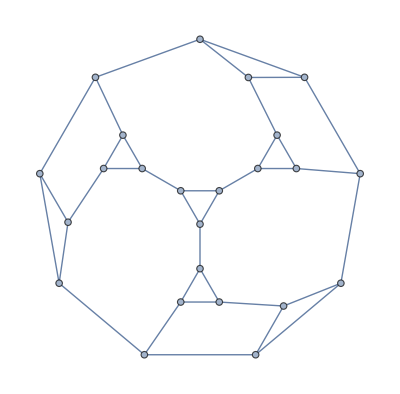
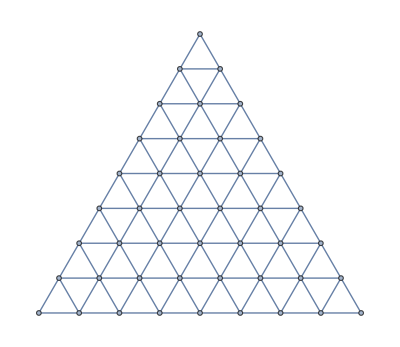
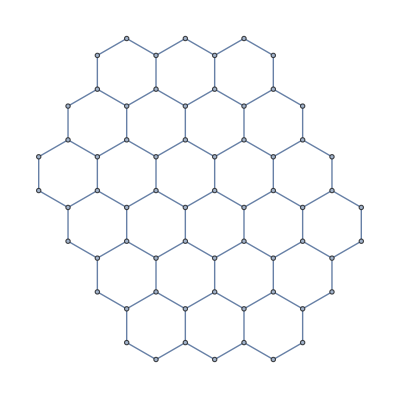
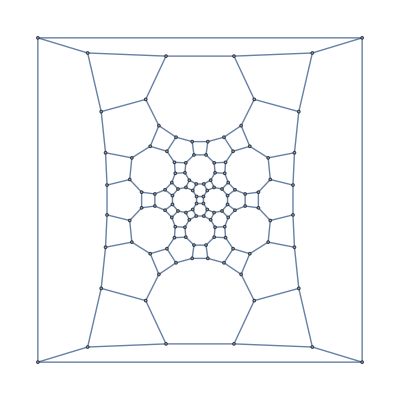
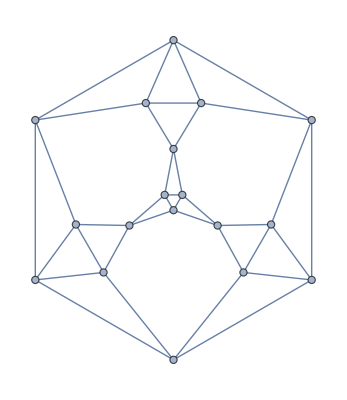
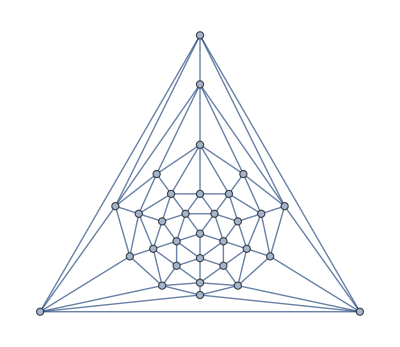
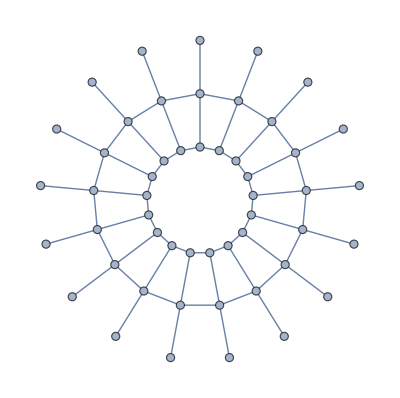
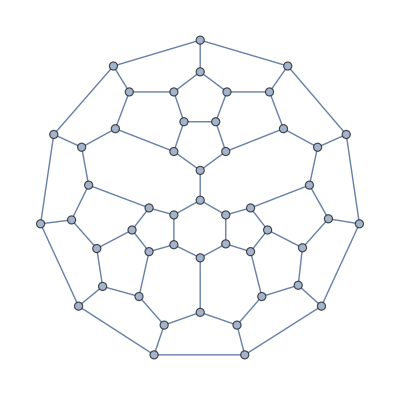
```mathematica
L={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

## Graph Matrices

### Exercise Subsection

A graph can be visualized in R^3 using the option VertexCoordinates:

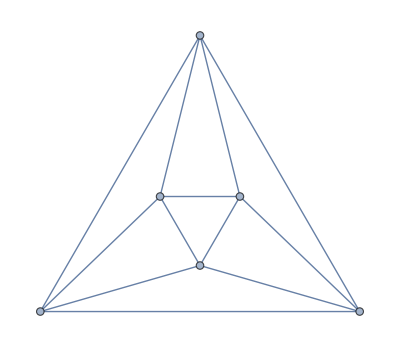
```mathematica
G=-Graphics-;
Graph[G,VertexCoordinates->{{-0.707,0,0},{0,0.048,-0.705},{0,0.705,0.048},{0,-0.705,-0.048},{0,-0.048,0.705},{0.707,0,0}}]
```

-Graphics3D-

The smallest eigenvalue for the KirchhoffMatrix is 0.  The next three smallest eigenvalues have eigenvectors that often provide good coordinates for vertex coordinates.  Do the following for the each of the graphs in list found in the next cell:

1. Find the three eigenvectors {x_1,x_2,x_3,...},  {y_1,y_2,y_3,...},  {z_1,z_2,z_3,...} that correspond to the smallest nonzero eigenvalues for KirchhoffMatrix.
2. Display the graph with vertex coordinates {{x_1,y_1,z_1},{x_2,y_2,z_2},{x_3,y_3,z_3}, ...}

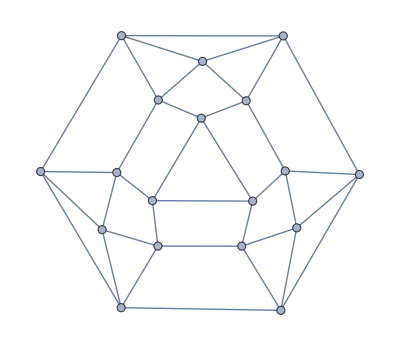
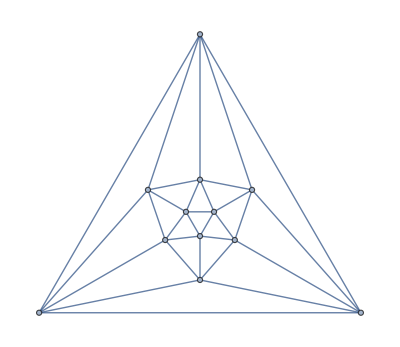
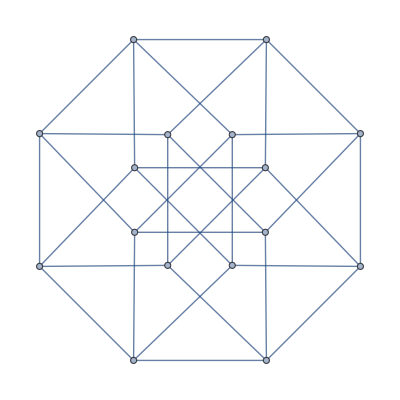
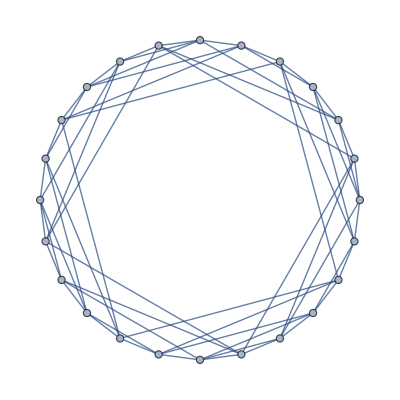
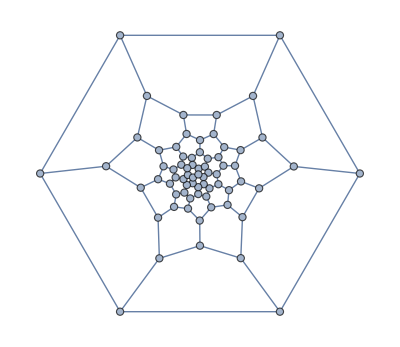
```mathematica
L={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```